```mathematica
β=2;ω0=2*Pi;
```

```mathematica
G[ω_]:=ω0^2/((ω0^2 - ω^2)+I*β*ω);
```

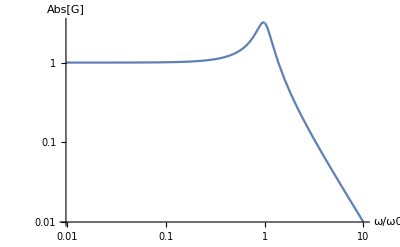

```mathematica
LogLogPlot[Abs[G[a*ω0]],{a,0,10}, PlotRange->Full, AxesLabel->{ω/"ω0",Abs[G]}]
```

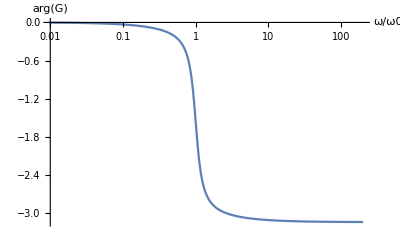

```mathematica
LogLinearPlot[Arg[G[a*ω0]],{a,0.01,200},AxesLabel->{ω/"ω0",Arg[G]},Exclusions->None]
```

```mathematica
GG[ω_]:=ω1^2/((ω1^2 - ω^2)+I*β1*ω);
```

```mathematica
Limit[Abs[GG[ω]],ω -> ω1]
```

Abs[ω1/β1]

```mathematica
Abs[GG[ω1]]
```

Abs[ω1/β1]

```mathematica
Arg[GG[ω1]]
```

Arg[-(ⅈ ω1)/β1]

Setting Ki, Kp relative to Kd as below basically turns the system (DDSHO, which is 2nd order) into a low-pass filter (first-order). The resonance (pole of K[omega]*G[omega]) is removed. K[omega]*G[omega] is now -i*I/omega.

```mathematica
Kd=0;Kp=100;Ki=0;
```

```mathematica
Kd=1;Kp=β*Kd;Ki=ω0^2*Kd;
```

```mathematica
K[ω_]:=Kp-I*Ki/ω+I*Kd*ω;T[ω_]:=G[ω]*K[ω]/(1+G[ω]*K[ω]);
```

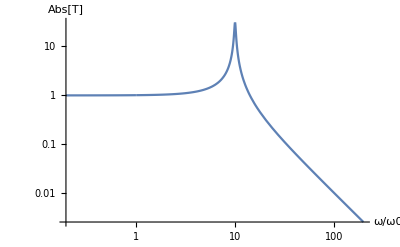

```mathematica
LogLogPlot[Abs[T[a*ω0]],{a,0,200},AxesLabel->{ω/"ω0",Abs[T]}]
```

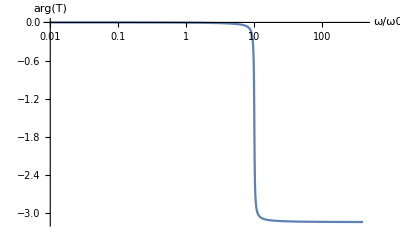

```mathematica
LogLinearPlot[Arg[T[a*ω0]],{a,0.01,400},PlotRange->Full,AxesLabel->{ω/"ω0",Arg[T]},Exclusions->None]
```

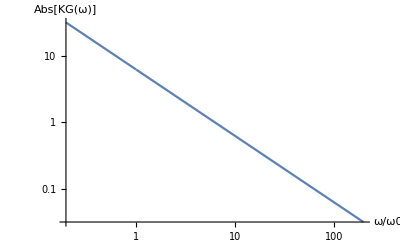

```mathematica
LogLogPlot[Abs[K[a*ω0]*G[a*ω0]],{a,0,200},AxesLabel->{ω/"ω0",Abs[KG[ω]]}]
```

```mathematica
LogLinearPlot[Arg[K[a*ω0]*G[a*ω0]],{a,0.01,400},PlotRange->Full,AxesLabel->{ω/"ω0",Arg[KG[ω]]},Exclusions->None]
```

-Graphics-

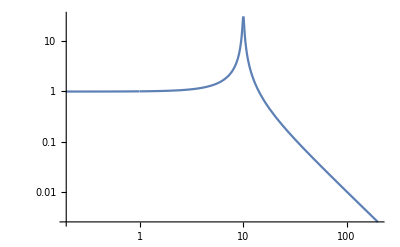

```mathematica
LogLogPlot[Abs[F[a*ω0]],{a,0,200}]
```

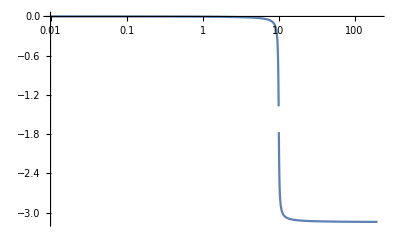

```mathematica
LogLinearPlot[Arg[F[a*ω0]],{a,0.01,200},PlotRange->Full]
```

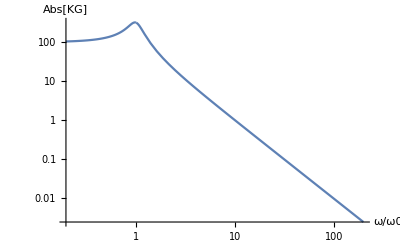

```mathematica
LogLogPlot[Abs[K[a*ω0]*G[a*ω0]],{a,0,200},AxesLabel->{ω/"ω0",Abs[KG]}]
```

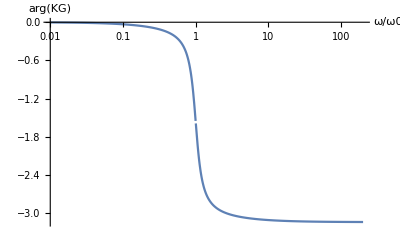

```mathematica
LogLinearPlot[Arg[K[a*ω0]*G[a*ω0]],{a,0.01,200},PlotRange->Full,AxesLabel->{ω/"ω0",Arg[KG]}]
```

```mathematica
β=2;ω0=2*Pi;
```

```mathematica
G[ω_]:=ω0^2/((ω0^2 - ω^2)+I*β*ω);
```

```mathematica
LogLogPlot[Abs[G[a*ω0]],{a,0,10}, PlotRange->Full, AxesLabel->{ω/"ω0",Abs[G]}]
```

-Graphics-

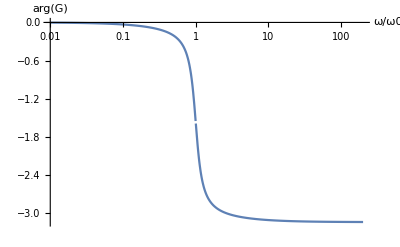

```mathematica
LogLinearPlot[Arg[G[a*ω0]],{a,0.01,200},AxesLabel->{ω/"ω0",Arg[G]}]
```